Exercises for Section 30 | Rearranging Lists

Use Thread to make a list of rules with each letter of the alphabet going to its position in the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Thread[Alphabet[]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

Make a 4×6 grid of the first 24 letters of the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Partition[Take[Alphabet[],24],4]//Grid
```

a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p
q | r | s | t
u | v | w | x

```mathematica
Partition[Take[Alphabet[],24],6]//Grid
```

a | b | c | d | e | f
g | h | i | j | k | l
m | n | o | p | q | r
s | t | u | v | w | x

Make a grid of the digits in 2^1000, with 50 digits per row, and put frames around everything. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Grid[Partition[IntegerDigits[2^1000],50],Frame->All]
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

Make a grid of the first 400 characters in the Wikipedia article for “computers”, with 20 characters per row, and frames around everything. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Grid[Partition[Characters[StringTake[WikipediaData["computers"],400]],20],Frame->All]
```

A |   | c | o | m | p | u | t | e | r |   | i | s |   | a |   | d | i | g | i
t | a | l |   | e | l | e | c | t | r | o | n | i | c |   | m | a | c | h | i
n | e |   | t | h | a | t |   | c | a | n |   | b | e |   | p | r | o | g | r
a | m | m | e | d |   | t | o |   | c | a | r | r | y |   | o | u | t |   | s
e | q | u | e | n | c | e | s |   | o | f |   | a | r | i | t | h | m | e | t
i | c |   | o | r |   | l | o | g | i | c | a | l |   | o | p | e | r | a | t
i | o | n | s |   | ( | c | o | m | p | u | t | a | t | i | o | n | ) |   | a
u | t | o | m | a | t | i | c | a | l | l | y | . |   | M | o | d | e | r | n
  | c | o | m | p | u | t | e | r | s |   | c | a | n |   | p | e | r | f | o
r | m |   | g | e | n | e | r | i | c |   | s | e | t | s |   | o | f |   | o
p | e | r | a | t | i | o | n | s |   | k | n | o | w | n |   | a | s |   | p
r | o | g | r | a | m | s | . |   | T | h | e | s | e |   | p | r | o | g | r
a | m | s |   | e | n | a | b | l | e |   | c | o | m | p | u | t | e | r | s
  | t | o |   | p | e | r | f | o | r | m |   | a |   | w | i | d | e |   | r
a | n | g | e |   | o | f |   | t | a | s | k | s | . |   | A |   | c | o | m
p | u | t | e | r |   | s | y | s | t | e | m |   | i | s |   | a |   | " | c
o | m | p | l | e | t | e | " |   | c | o | m | p | u | t | e | r |   | t | h
a | t |   | i | n | c | l | u | d | e | s |   | t | h | e |   | h | a | r | d
w | a | r | e | , |   | o | p | e | r | a | t | i | n | g |   | s | y | s | t
e | m |   | ( | m | a | i | n |   | s | o | f | t | w | a | r | e | ) | , |

Make a line plot of the flattened list of the digits from the numbers from 0 to 200 (Champernowne sequence). |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[0,200]]]]
```

-Graphics-

Make 4 steps in the “Menger sponge” analog of the fractal Sierpinski pattern from the text, but with a “kernel” of the form {{#,#,#},{#,0,#},{#,#,#}}. |

EXPECTED OUTPUT »

-Graphics- | ×


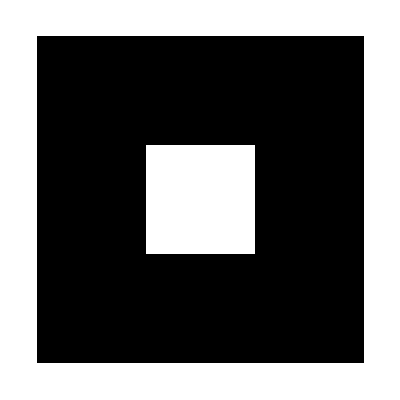
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot /@ NestList[ArrayFlatten[{{#, #,#}, {#, 0,#},{#,#,#}}] &, {{1}}, 4]
```

Find Pythagorean triples involving only integers by selecting {x,y,Sqrt[x^2+y^2]} with x and y up to 20. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[{x,y,Sqrt[x^2+y^2]},{x,20},{y,20}]
```

{{{1,1,√2},{1,2,√5},{1,3,√10},{1,4,√17},{1,5,√26},{1,6,√37},{1,7,5 √2},{1,8,√65},{1,9,√82},{1,10,√101},{1,11,√122},{1,12,√145},{1,13,√170},{1,14,√197},{1,15,√226},{1,16,√257},{1,17,√290},{1,18,5 √13},{1,19,√362},{1,20,√401}},18,{{20,1,√401},{20,2,2 √101},16,{20,19,√761},{20,20,20 √2}}}
 |  |  |  |

```mathematica
Array[{#1,#2,#3}&,{{Range[20]},{Range[20]}}]
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[{#1,#2,#3}&,{{{1,2,3,4,5,6,7,8,9,10,«10»}},{{1,2,3,4,5,6,7,8,9,10,«10»}}}].

Array[{#1,#2,#3}&,{{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}}}]

```mathematica
Array[If[#1 == #2, x, #1*#2] &, {5, 5}] // Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

```mathematica
FoldList[{#1,#2} &, x, Range[5]]
```

{x,{x,1},{{x,1},2},{{{x,1},2},3},{{{{x,1},2},3},4},{{{{{x,1},2},3},4},5}}

```mathematica
Select[Flatten[Table[fnc, x, y], 1], 
 IntegerQ[Last[#]] &]
```

```mathematica
Select[Flatten[Table[{x,y,Sqrt[x^2+y^2]},{x,20},{y,20}],1],IntegerQ[Last@#]&]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}

Find the lengths of the longest sequences of identical digits in 2^n for n up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Split[Flatten[IntegerDigits[Table[2^n,{n,100}]]]]
```

{{2},{4},{8},{1},{6},{3},{2},{6},{4},{1},{2},{8},{2},{5},{6},{5},{1},{2},{1},{0},{2},{4},{2},{0},{4},{8},{4},{0},{9},{6},{8},{1},1369,{0},{2},{6},{8,8},{1},{2},{6},{7},{6},{5},{0},{6},{0,0},{2,2},{8},{2,2},{9},{4},{0},{1},{4},{9},{6},{7},{0},{3},{2},{0},{5},{3},{7},{6}}
 |  |  |  |

```mathematica
Length /@ Split[IntegerDigits[2^n]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
IntegerDigits[2^50]
Length/@Split[IntegerDigits[2^50]]
```

{1,1,2,5,8,9,9,9,0,6,8,4,2,6,2,4}

{2,1,1,1,3,1,1,1,1,1,1,1,1}

```mathematica
Table[Max[Length/@Split[IntegerDigits[2^n]]],{n,100}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

Take the names of integers up to 100 and gather them into sublists according to their first letters. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GatherBy[Table[IntegerName[n],{n,100}],StringTake[#,1]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

```mathematica
GatherBy[Array[IntegerName,100],StringTake[#,1]]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine,one hundred}

Sort the first 50 words in WordList[ ] by their last letters. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
SortBy[Take[WordList[],50],StringTake[#,-1]&]
```

{a,abandoned,abashed,abbreviated,abed,abalone,abase,abate,abbe,abbreviate,abdicate,abeyance,abhorrence,abidance,abide,abducting,abiding,aah,abash,aardvark,aback,abdominal,abeam,abandon,abbreviation,abdication,abdomen,abduction,aberration,abjection,abattoir,abductor,abettor,abhor,abacus,abbess,abaft,abandonment,abasement,abashment,abatement,abbot,abduct,aberrant,abet,abhorrent,abject,abbey,ability,abjectly}

Make a list of the first 20 squares, sorted by their first digits. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Array[#^2,20&]
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[#1^2,20&].

Array[#1^2,20&]

```mathematica
FromDigits/@SortBy[Table[IntegerDigits[x^2],{x,20}],First]
```

{1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9}

Sort integers up to 20 by the length of their names in English. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringLength/@IntegerName/@Range[20]
```

{3,3,5,4,4,3,5,5,4,3,6,6,8,8,7,7,9,8,8,6}

```mathematica
SortBy[Range[20],StringLength[IntegerName[#]]&]
```

{1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17}

```mathematica
SortBy[Range[20],StringLength/@IntegerName[#]&]
```

{8,18,11,15,5,4,14,9,19,1,7,17,6,16,10,13,3,12,20,2}

Get a random sample of 20 words from WordList[ ], and gather them into sublists by length. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GatherBy[RandomChoice[WordList[],20],StringLength]
```

{{unspoken,scaffold,relegate,conjurer},{retrenchment,illogicality},{idealistic,eisteddfod},{don,yuk},{precedent,stressful,eglantine},{sexist,unwrap,unison},{prang},{unequivocally},{depress},{gentlewoman}}

```mathematica
GatherBy[RandomChoice[WordList[],20],StringLength]
```

{{werewolf,affected,gardenia,dampener,shambles},{shill,rajah},{discouraging,chesterfield},{monopolist,corrigenda,kick-start},{contend,marquee},{laundress},{palpitating,distinction},{poncho,sevens},{seam}}

```mathematica
GatherBy[RandomSample[WordList[],20],StringLength]
```

{{philtre,inveigh,apricot},{returnable,restricted,allotropic},{perceivable,detestation,daydreaming},{bugler,schema,social},{nauseous,sprigged,attached,delegate},{sycophant,whitehead},{jean},{cauterization}}

Find letters that appear in Ukrainian but not Russian. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Complement[Alphabet["Ukrainian"],Alphabet["Russian"]]
```

{є,і,ї,ґ}

Use Intersection to find numbers that appear both among the first 100 squares and cubes. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Intersection[Table[x^2,{x,100}],Table[y^3,{y,100}]]
```

{1,64,729,4096}

```mathematica
Table[x^2,{x,100}]
Table[y^3,{y,100}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801,10000}

{1,8,27,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000,9261,10648,12167,13824,15625,17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,46656,50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,117649,125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,262144,274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,531441,551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,1000000}

Find the list of countries that are in both NATO and the G8. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Intersection[EntityList@EntityClass["Country","NATO"],EntityList@EntityClass["Country","GroupOf8"]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

```mathematica
EntityClass["Country","NATO"]
```

North Atlantic Treaty Organization

```mathematica
EntityList["NATO"]
```

Missing[UnknownType,NATO]

Make a grid in which all possible permutations of the numbers 1 through 4 appear as successive columns. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Grid[Transpose[Permutations[Range[4]]]]
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

Make a list of all the different strings that can be obtained by permuting the characters in “hello”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin/@Permutations[Characters["hello"]]
```

{hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lehlo,lehol,lelho,leloh,leohl,leolh,llheo,llhoe,lleho,lleoh,llohe,lloeh,lohel,lohle,loehl,loelh,lolhe,loleh,ohell,ohlel,ohlle,oehll,oelhl,oellh,olhel,olhle,olehl,olelh,ollhe,olleh}

```mathematica
Union[StringJoin/@Permutations[Characters["hello"]]]
```

{ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,lehlo,lehol,lelho,leloh,leohl,leolh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lleho,lleoh,llheo,llhoe,lloeh,llohe,loehl,loelh,lohel,lohle,loleh,lolhe,oehll,oelhl,oellh,ohell,ohlel,ohlle,olehl,olelh,olhel,olhle,olleh,ollhe}

```mathematica
Union[StringJoin /@ Permutations[Characters["hello"]]]
```

{ehllo,ehlol,eholl,elhlo,elhol,ellho,elloh,elohl,elolh,eohll,eolhl,eollh,hello,helol,heoll,hlelo,hleol,hlleo,hlloe,hloel,hlole,hoell,holel,holle,lehlo,lehol,lelho,leloh,leohl,leolh,lhelo,lheol,lhleo,lhloe,lhoel,lhole,lleho,lleoh,llheo,llhoe,lloeh,llohe,loehl,loelh,lohel,lohle,loleh,lolhe,oehll,oelhl,oellh,ohell,ohlel,ohlle,olehl,olelh,olhel,olhle,olleh,ollhe}

Make an array plot of the sequence of possible 5-tuples of 0 and 1. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ArrayPlot[Tuples[{0,1},5]]
```

-Graphics-

Generate a list of 10 random sequences of 5 letters. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[StringJoin[Table[RandomChoice[Alphabet[]],5]],10]
```

{bgadd,lmvjp,sltmh,mnmuq,xpjeo,jhugo,xubrt,kufle,czhlx,xmsfu}

```mathematica
StringJoin[Table[RandomChoice[Alphabet[]],5]]
```

rizyw

Find a simpler form for Flatten[Table[{i,j,k},{i,2},{j,2},{k,2}],2]. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Flatten[Table[{i,j,k},{i,2},{j,2},{k,2}
],2]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
Permutations[{1,1,2}]
```

{{1,1,2},{1,2,1},{2,1,1}}

```mathematica
uples
```

```mathematica
Combinations
```

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

Make an array plot from the numbers of the letters in the first 1000 characters in the Wikipedia article on “computers”, with 30 letters per row. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Take[Characters[WikipediaData["computers"]],1000]
```

{A, ,c,o,m,p,u,t,e,r, ,i,s, ,a, ,d,i,g,i,t,a,l, ,e,l,e,c,t,r,o,n,i,c, ,m,a,c,h,i,n,e, ,t,h,a,t, ,c,a,n, ,b,e, ,p,r,o,g,r,a,m,m,e,d, ,t,o, ,c,a,r,r,y, ,o,u,t, ,s,e,q,u,e,n,c,e,s, ,o,f, ,a,r,i,t,h,m,e,t,i,c, ,o,r, ,l,o,g,i,c,a,l, ,o,p,e,r,a,t,i,o,n,s, ,(,c,o,m,p,u,t,a,t,i,o,n,), ,a,u,t,o,m,a,t,i,c,a,l,l,y,., ,M,o,d,e,r,n, ,c,o,m,p,u,t,e,r,s, ,c,a,n, ,p,e,r,f,o,r,m, ,g,e,n,e,r,i,c, ,s,e,t,s, ,o,f, ,o,p,e,r,a,t,i,o,n,s, ,k,n,o,w,n, ,a,s, ,p,r,o,g,r,a,m,s,., ,T,h,e,s,e, ,p,r,o,g,r,a,m,s, ,e,n,a,b,l,e, ,c,o,m,p,u,t,e,r,s, ,t,o, ,p,e,r,f,o,r,m, ,a, ,w,i,d,e, ,r,a,n,g,e, ,o,f, ,t,a,s,k,s,., ,A, ,c,o,m,p,u,t,e,r, ,s,y,s,t,e,m, ,i,s, ,a, ,",c,o,m,p,l,e,t,e,", ,c,o,m,p,u,t,e,r, ,t,h,a,t, ,i,n,c,l,u,d,e,s, ,t,h,e, ,h,a,r,d,w,a,r,e,,, ,o,p,e,r,a,t,i,n,g, ,s,y,s,t,e,m, ,(,m,a,i,n, ,s,o,f,t,w,a,r,e,),,, ,a,n,d, ,p,e,r,i,p,h,e,r,a,l, ,e,q,u,i,p,m,e,n,t, ,n,e,e,d,e,d, ,a,n,d, ,u,s,e,d, ,f,o,r, ,",f,u,l,l,", ,o,p,e,r,a,t,i,o,n,., ,T,h,i,s, ,t,e,r,m, ,m,a,y, ,a,l,s,o, ,r,e,f,e,r, ,t,o, ,a, ,g,r,o,u,p, ,o,f, ,c,o,m,p,u,t,e,r,s, ,t,h,a,t, ,a,r,e, ,l,i,n,k,e,d, ,a,n,d, ,f,u,n,c,t,i,o,n, ,t,o,g,e,t,h,e,r,,, ,s,u,c,h, ,a,s, ,a, ,c,o,m,p,u,t,e,r, ,n,e,t,w,o,r,k, ,o,r, ,c,o,m,p,u,t,e,r, ,c,l,u,s,t,e,r,.,
,A, ,b,r,o,a,d, ,r,a,n,g,e, ,o,f, ,i,n,d,u,s,t,r,i,a,l, ,a,n,d, ,c,o,n,s,u,m,e,r, ,p,r,o,d,u,c,t,s, ,u,s,e, ,c,o,m,p,u,t,e,r,s, ,a,s, ,c,o,n,t,r,o,l, ,s,y,s,t,e,m,s,., ,S,i,m,p,l,e, ,s,p,e,c,i,a,l,-,p,u,r,p,o,s,e, ,d,e,v,i,c,e,s, ,l,i,k,e, ,m,i,c,r,o,w,a,v,e, ,o,v,e,n,s, ,a,n,d, ,r,e,m,o,t,e, ,c,o,n,t,r,o,l,s, ,a,r,e, ,i,n,c,l,u,d,e,d,,, ,a,s, ,a,r,e, ,f,a,c,t,o,r,y, ,d,e,v,i,c,e,s, ,l,i,k,e, ,i,n,d,u,s,t,r,i,a,l, ,r,o,b,o,t,s, ,a,n,d, ,c,o,m,p,u,t,e,r,-,a,i,d,e,d, ,d,e,s,i,g,n,,, ,a,s, ,w,e,l,l, ,a,s, ,g,e,n,e,r,a,l,-,p,u,r,p,o,s,e, ,d,e,v,i,c,e,s, ,l,i,k,e, ,p,e,r,s,o,n,a,l, ,c,o,m,p,u,t,e,r,s, ,a,n,d, ,m,o,b,i,l,e, ,d,e,v,i,c,e,s, ,l,i,k,e, ,s,m,a,r,t,p,h,o,n,e,s,., ,C,o,m,p,u,t,e,r,s, ,p,o,w,e,r, ,t,h,e, ,I,n,t,e,r,n,e,t,,, ,w,h,i,c,h, ,l,i,n,k,s, ,b,i,l,l,i,o,n,s, ,o,f, ,o,t,h,e,r, ,c,o}

```mathematica
]
```

```mathematica
ArrayPlot[
 Partition[
  LetterNumber /@ Take[Characters[WikipediaData["computers"]], 1000], 
  30]]
```

-Graphics-

```mathematica
ArrayPlot[
 Partition[
  LetterNumber [ 
   Take[Select[Characters[WikipediaData["computers"]], LetterQ], 
    1000], 30]]
```

-Graphics-

```mathematica
ArrayPlot[
 Partition[
  LetterNumber[
   Take[Select[Characters[WikipediaData["computers"]], LetterQ], 
    1000]], 30]]
```

-Graphics-

Gather integers up to 30 into lists based on their values modulo 3. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GatherBy[Range[30],Mod[#,3]&]
```

{{1,4,7,10,13,16,19,22,25,28},{2,5,8,11,14,17,20,23,26,29},{3,6,9,12,15,18,21,24,27,30}}

Gather the first 50 powers of 2 according to their last digits. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
GatherBy[Table[2^x,{x,50}],Last[IntegerDigits[#]]&]
```

{{2,32,512,8192,131072,2097152,33554432,536870912,8589934592,137438953472,2199023255552,35184372088832,562949953421312},{4,64,1024,16384,262144,4194304,67108864,1073741824,17179869184,274877906944,4398046511104,70368744177664,1125899906842624},{8,128,2048,32768,524288,8388608,134217728,2147483648,34359738368,549755813888,8796093022208,140737488355328},{16,256,4096,65536,1048576,16777216,268435456,4294967296,68719476736,1099511627776,17592186044416,281474976710656}}

```mathematica
Table[2^x,{x,50}]
```

{2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288,1048576,2097152,4194304,8388608,16777216,33554432,67108864,134217728,268435456,536870912,1073741824,2147483648,4294967296,8589934592,17179869184,34359738368,68719476736,137438953472,274877906944,549755813888,1099511627776,2199023255552,4398046511104,8796093022208,17592186044416,35184372088832,70368744177664,140737488355328,281474976710656,562949953421312,1125899906842624}

Make a line plot of the result of sorting the numbers from −10 to +10 by their absolute values. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[SortBy[Range[-10,10],Abs[#]&]]
```

-Graphics-

```mathematica
Range[-10]
```

{}

```mathematica
Join[-Range[10],Range[10]]
Range[-10,10]
```

{-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,1,2,3,4,5,6,7,8,9,10}

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Make a line plot of the list of the first 200 squares, sorted by their first digits. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[SortBy[Table[x^2,{x,200}],First[IntegerDigits[#]]&]]
```

-Graphics-

Make a line plot of integers up to 200 sorted by the lengths of their names in English. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[SortBy[Range[200],StringLength[IntegerName[#]]&]]
```

-Graphics-

```mathematica
Sort[StringLength/@Table[IntegerName[n],{n,200}]]
```

{3,3,3,3,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,7,7,7,8,8,8,8,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,15,15,15,15,16,16,16,17,17,17,17,17,17,18,18,18,18,18,18,19,19,19,20,20,20,20,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25}

Get a random sample of 25 words from WordList[]. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
RandomSample[WordList[],25]
```

{minty,stratosphere,alcoholism,butane,divergence,mastered,existent,bike,recording,notched,somberly,personnel,subsidiary,piecework,googly,keyed,predictability,alpine,sirree,soybean,adducing,placidity,paraphernalia,shade,rename}

Riffle periods into the string “UNCLE” to make “U.N.C.L.E.”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
StringJoin[Riffle[Characters["UNCLE"],"."],"."]
```

U.N.C.L.E.

Find letters that appear in Swedish or Polish but not English. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Complement[Union[Alphabet["Swedish"],Alphabet["Polish"]],Alphabet[]]
```

{ą,ę,ń,ś,ź,ż,å,ä,ć,ł,ó,ö}

Find countries that are in the World Health Organization but not the United Nations. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Complement[EntityList[EntityClass["Country","WorldHealthOrganization"]],EntityList[EntityClass["Country","UnitedNations"]]]
```

{Cook Islands,Niue}

Make a list of all pair-wise blends of red, green and blue. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Blend/@Tuples[{Red,Green,Blue},2]
```

{RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]}

Make a list of array plots, each 50 rows high and with image size 50, of successive possible 8-tuples of 0 and 1. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Tuples[{0,1},8]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,1},{0,0,0,0,0,1,0,0},{0,0,0,0,0,1,0,1},{0,0,0,0,0,1,1,0},242,{1,1,1,1,1,0,0,1},{1,1,1,1,1,0,1,0},{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1}}
 |  |  |  |

```mathematica
ArrayPlot[#, ImageSize -> 50] & /@ Partition[Tuples[{0, 1}, 8], 50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Generate 1000 random sequences of 4 letters, and make a list of ones that appear in WordList[ ].  |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Intersection[Table[StringJoin[RandomChoice[Alphabet[],4]],1000],WordList[]]
```

{boar,bran,chop,surf,tort,town}

```mathematica
Random
```